## Audio Project

```mathematica
Import["/Users/aarnav/Downloads/PinkPanther30.wav"]
```

```mathematica
dt2=AudioData[Import["/Users/aarnav/Downloads/PinkPanther30.wav"]];
```

```mathematica
Dimensions[dt2]
```

{1,50001}

```mathematica
dt2
```

{{0.466095,0.509583,0.539398,0.555115,0.548828,0.523132,0.487244,0.441833,0.386719,0.326874,0.262115,0.189148,0.11438,0.0461426,49973,-0.294434,-0.21701,-0.140289,-0.0767517,-0.0314026,-0.0111694,-0.019043,-0.0524902,-0.10791,-0.177521,-0.254181,-0.332245,-0.399628,-0.445557}}
 |  |  |  |

```mathematica
MatrixForm[dt2[[All,;;20]]]
```

(0.000488281 | 0.000488281 | 0.000488281 | 0.000488281 | 0.000488281 | 0.000488281 | 0.000518799 | 0.000457764 | 0.000488281 | 0.000457764 | 0.000457764 | 0.000427246 | 0.000488281 | 0.000457764 | 0.000457764 | 0.000457764 | 0.000457764 | 0.000518799 | 0.000457764 | 0.000488281)

```mathematica
bach50=dt2[[1]];
```

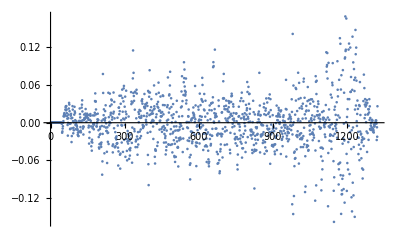

```mathematica
ListPlot[bach50[[;;;;500]]]
```

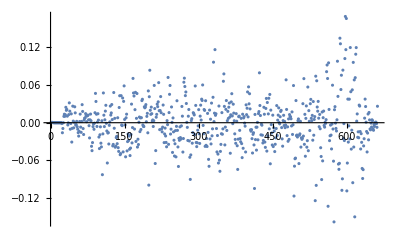

```mathematica
ListPlot[bach50[[;;;;1000]]]
```

```mathematica
Manipulate[Plot[Sum[bach50[[Max[1,Min[50000,Round[50000/6.25*(n*T)]]]]]Sinc[Pi*(t/T-n)],{n,Floor[6.25/T]}],{t,0,6.25},PlotRange->{-.08,.08}],{{T,1},.0001,6}]
```

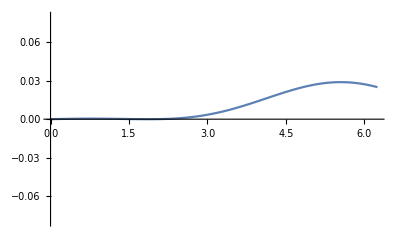
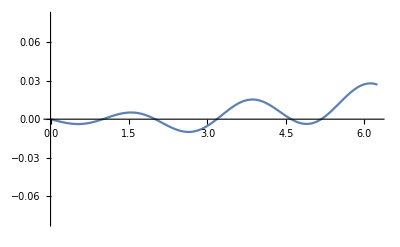
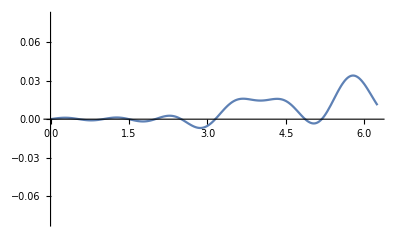
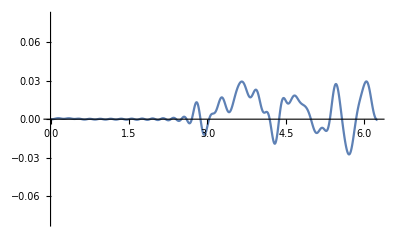
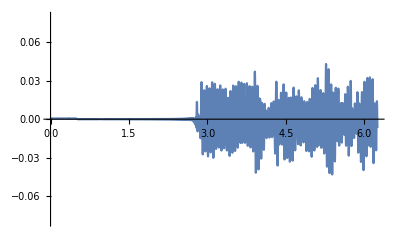
3 | -Graphics-
6 | -Graphics-
12 | -Graphics-
62 | -Graphics-
625 | -Graphics-

```mathematica
Grid[Table[{Floor[6.25/T],Plot[Evaluate[Sum[bach50[[Max[1,Min[50000,Round[50000/6.25*(n*T)]]]]]Sinc[Pi*(t/T-n)],{n,Floor[6.25/T]}]],{t,0,6.25},PlotRange->{-.08,.08}]},{T,{2,1,.5,.1,.01}}]]
```

```mathematica
ByteCount[%]
```

175536

```mathematica
Spectrogram[bach50,PlotRange->{0,.1}]
```

-Graphics-

## Equidistribution of irrational multiples

```mathematica
ϕ=GoldenRatio;
```

```mathematica
N[ϕ,100]
```

1.618033988749894848204586834365638117720309179805762862135448622705260462818902449707207204189391137

```mathematica
ϕ^2==ϕ+1
```

True

```mathematica
y=Sqrt[2];
```

```mathematica
N[y,100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

### Fractional Part

```mathematica
N[Mod[ϕ,1]]
```

0.618034

```mathematica
N[Mod[y,1]]
```

0.414214

### Table

```mathematica
Grid[Prepend[{Row[{n,Sqrt[2]}],"mod 1"}][Table[{Row[{n,Sqrt[2]}],N[Mod[n*y,1]]},{n,10}]],Frame->All,Background->{None,{LightGray,None}}]
```

n√2 | mod 1
1√2 | 0.414214
2√2 | 0.828427
3√2 | 0.242641
4√2 | 0.656854
5√2 | 0.0710678
6√2 | 0.485281
7√2 | 0.899495
8√2 | 0.313708
9√2 | 0.727922
10√2 | 0.142136

```mathematica
Manipulate[NumberLinePlot[{N[Mod[Range[n-1]*y,1]],{N[Mod[n*y,1]]}},PlotRange->{0,1}],{n,1,100,1}]
```

```mathematica
Manipulate[Graphics[{{Blue,Point[ReIm[Exp[2Pi*I*N[Mod[Range[n-1]*Sqrt[2],1]]]]]},{Red,Point[ReIm[Exp[2Pi*I*N[Mod[n*Sqrt[2],1]]]]]}},PlotRange->1.6],{n,1,200,1}]
```

```mathematica
Manipulate[BlockRandom[SeedRandom[30];Graphics[{{Blue,Point[ReIm[Exp[2Pi*I*N[Mod[#[[;;n-1]],1]]]]]},{Red,Point[ReIm[Exp[2Pi*I*N[Mod[#[[n]],1]]]]]}},PlotRange->1.6]&[RandomReal[1,200]]],{n,1,200,1}]
```

```mathematica
y
```

√2

```mathematica
Table[n*y,{n,1,100}]
```

{√2,2 √2,3 √2,4 √2,5 √2,6 √2,7 √2,8 √2,9 √2,10 √2,11 √2,12 √2,13 √2,14 √2,15 √2,16 √2,17 √2,18 √2,19 √2,20 √2,21 √2,22 √2,23 √2,24 √2,25 √2,26 √2,27 √2,28 √2,29 √2,30 √2,31 √2,32 √2,33 √2,34 √2,35 √2,36 √2,37 √2,38 √2,39 √2,40 √2,41 √2,42 √2,43 √2,44 √2,45 √2,46 √2,47 √2,48 √2,49 √2,50 √2,51 √2,52 √2,53 √2,54 √2,55 √2,56 √2,57 √2,58 √2,59 √2,60 √2,61 √2,62 √2,63 √2,64 √2,65 √2,66 √2,67 √2,68 √2,69 √2,70 √2,71 √2,72 √2,73 √2,74 √2,75 √2,76 √2,77 √2,78 √2,79 √2,80 √2,81 √2,82 √2,83 √2,84 √2,85 √2,86 √2,87 √2,88 √2,89 √2,90 √2,91 √2,92 √2,93 √2,94 √2,95 √2,96 √2,97 √2,98 √2,99 √2,100 √2}

```mathematica
N[Mod[Table[n*y,{n,1,100}],1]]
```

{0.414214,0.828427,0.242641,0.656854,0.0710678,0.485281,0.899495,0.313708,0.727922,0.142136,0.556349,0.970563,0.384776,0.79899,0.213203,0.627417,0.0416306,0.455844,0.870058,0.284271,0.698485,0.112698,0.526912,0.941125,0.355339,0.769553,0.183766,0.59798,0.0121933,0.426407,0.84062,0.254834,0.669048,0.0832611,0.497475,0.911688,0.325902,0.740115,0.154329,0.568542,0.982756,0.39697,0.811183,0.225397,0.63961,0.0538239,0.468037,0.882251,0.296465,0.710678,0.124892,0.539105,0.953319,0.367532,0.781746,0.195959,0.610173,0.0243866,0.4386,0.852814,0.267027,0.681241,0.0954544,0.509668,0.923882,0.338095,0.752309,0.166522,0.580736,0.994949,0.409163,0.823376,0.23759,0.651804,0.0660172,0.480231,0.894444,0.308658,0.722871,0.137085,0.551299,0.965512,0.379726,0.793939,0.208153,0.622366,0.0365799,0.450793,0.865007,0.279221,0.693434,0.107648,0.521861,0.936075,0.350288,0.764502,0.178716,0.592929,0.00714267,0.421356}

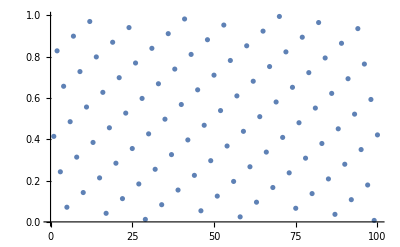

```mathematica
ListPlot[N[Mod[Table[n*y,{n,1,100}],1]]]
```

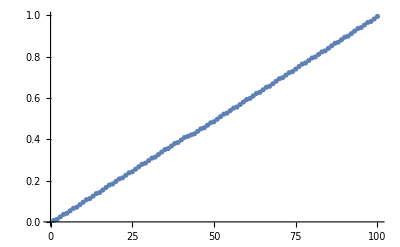

```mathematica
ListPlot[Sort[N[Mod[Table[n*y,{n,1,100}],1]]]]
```

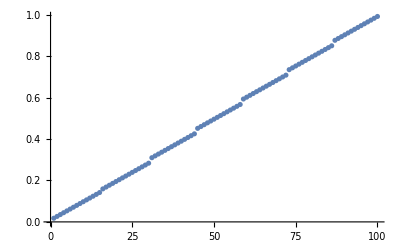

```mathematica
ListPlot[Sort[N[Mod[Table[n*Pi,{n,1,100}],1]]]]
```

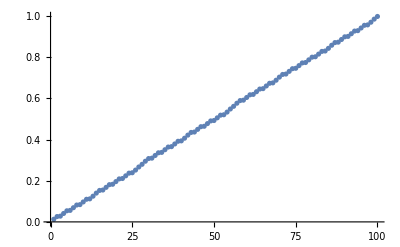

```mathematica
ListPlot[Sort[N[Mod[Table[n*E,{n,1,100}],1]]]]
```

```mathematica
ContinuedFraction[E,20]
```

{2,1,2,1,1,4,1,1,6,1,1,8,1,1,10,1,1,12,1,1}

```mathematica
ContinuedFraction[Pi,20]
```

{3,7,15,1,292,1,1,1,2,1,3,1,14,2,1,1,2,2,2,2}

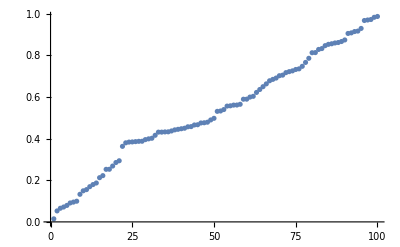

```mathematica
ListPlot[Sort[RandomReal[1,100]]]
```

```mathematica
Integrate[x,{x,0,1}]
```

1/2

```mathematica
Mean[N[Mod[Table[n*y,{n,1,100}],1]]]
```

0.497785

```mathematica
Mean[N[Mod[Table[n*Pi,{n,1,100}],1]]]
```

0.500429

```mathematica
Mean[RandomReal[1,100]]
```

0.548397

```mathematica
N[Integrate[x^100,{x,0,1}]]
```

0.00990099

```mathematica
Mean[RandomReal[1,100]^100]
```

0.0154447

```mathematica
Mean[N[Mod[Table[n*y,{n,1,100}],1]]^100]
```

0.00871179

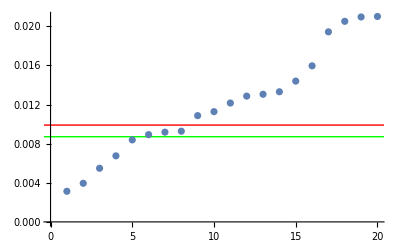

```mathematica
ListPlot[Sort[Table[Mean[RandomReal[1,100]^100],20]],Epilog->{{Green,InfiniteLine[{0,Mean[N[Mod[Table[n*y,{n,1,100}],1]]^100]},{1,0}]},{Red,InfiniteLine[{0,1/101},{1,0}]}}
]
```

## Function Names in other software

Matlab:  audioread, plot

Python:  audio2numpy  (lots of alternatives)  plot (matplotlib)